# Lab 10: Yahtzee

In this lab, we will solve some problems about rolling dice.

### Rules:

In Yahtzee, each player has  dice. They would like to roll any of the following patterns, which give them the following scores. They can roll the dice, then re-roll any that they wish. They can re-roll again. This means that they have 3 rolls in total.

### Example gameplay

Suppose that we want to score as many points as possible, by using any category.

We first roll 4, 1, 3, 6, 6.

Then, we decide that we want to re-roll the 4,1,3.

Now we have 4,6,3,6,6

We re-roll the 4 and 3.

We end with 4,5,6,6,6, which is worth  points from the sixes category.

### Dice simulator

Here is a simulator that rolls 6 dice.

```mathematica
diceRolls = RandomInteger[{1,6},5] (*Simulates rolling 5 dice*)
```

{1,6,6,4,5}

### Hand validator

These functions evaluate hands based on categories.

```mathematica
value[num_,hand_]:= Total[Select[hand, (#==num &)]]
value[5,{2,3,5,5,6}] (*should give 10*)
threeOfAKind[hand_]:=If[AnyTrue[Tally[hand], (#[[2]]>=3&)],Total[hand],0];
threeOfAKind[{2,1,5,5,2,6}] (*Should give 0*)
fourOfAKind[hand_]:=If[AnyTrue[Tally[hand], (#[[2]]>=4&)],Total[hand],0];
fullHouse[hand_]:=If[Length[Tally[hand]]==2, 25,0];
longestRun[list_List]:=Module[{s,groups},s=Sort@DeleteDuplicates[list];
If[s==={},Return[{}]];
groups=Split[s,(#2==#1+1)&];
First@MaximalBy[groups,Length]](*This function was generated by ChatGPT.*)
smallStraight [hand_] :=If[Length[longestRun[hand]]>=4,30,0];
largeStraight[hand_]:= If[Length[longestRun[hand]]==5,40,0];
yahtzee[hand_]:= If[Length[Tally[hand]]==1, 50,0];
```

10

0

## First Questions:

For each category, what is the expected value of that category when all 5 dice are rolled once?
-The lower category is simple
-Three of a kind and four of a kind seem tricky. Direct counting?
-Full house, small/large straight, yahtzee reduce to calculating probabilities.

### Simulations

Here are some simulations of rolling all 5 dice once, then calculating a score for a given category. We give the average number of points scored.

```mathematica
N[Mean[Table[value[1, RandomInteger[{1,6},5]],{10000}]]] (*The average over 10 trials if we roll once and count aces. *)
```

0.8364

```mathematica
N[Mean[Table[threeOfAKind[ RandomInteger[{1,6},5]],{10000}]]]
```

3.68468

```mathematica
N[Mean[Table[largeStraight[ RandomInteger[{1,6},5]],{10000}]]]
```

1.2224

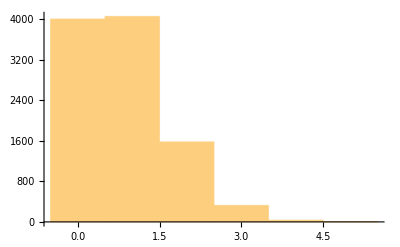

```mathematica
Histogram[Table[value[1,RandomInteger[{1,6},5]],{10000}],{1}]
```

## Using Rerolls

1.) Now we want to consider rerolling the dice.
These questions all involve a rerolling strategy.
If we want to get the “value” category, we reroll the dice that are not of that value.
What is the expected value of 3 rolls, if we’re going for Aces?

2.) Now suppose that we want 3 of a kind. Suppose that we roll the dice. 
Whenever we have multiple of the same number, we keep them, otherwise reroll them.
What is the probability that we can get 3 of a kind?

What is the expected value of this strategy for 3 of a kind?

3.) Suppose we adopt a different re-roll strategy, seeking 3 of a kind. Whenever all the dice are different, we keep the largest value, then reroll the rest. Otherwise, follow the strategy from 2.) Will this strategy change the probability of getting 3 of a kind? Will it change the expected value?

```mathematica
reroll[hand_List,criterion_]:=Module[{newHand=hand},newHand=Table[If[criterion[i,hand],hand[[i]],(*keep this die*)RandomInteger[{1,6}]      (*re-roll*)],{i,Length[hand]}];
newHand]
```

```mathematica
hand={6,3,2,6,1};
reroll[hand,Function[{i,h},h[[i]]==6]]
(*Example output:{6,5,4,6,2}*)
```

{6,1,6,6,1}

```mathematica
rerollNTimes[n_,hand_,criterion_]:=Module[{currentHand,counter}, currentHand = hand;counter=1; While[counter<=n, counter++;currentHand = reroll[currentHand,criterion];];currentHand]
```

```mathematica
rerollNTimes[3,{6,3,2,6,1},Function[{i,h},h[[i]]==6]]
```

{6,1,6,6,1}

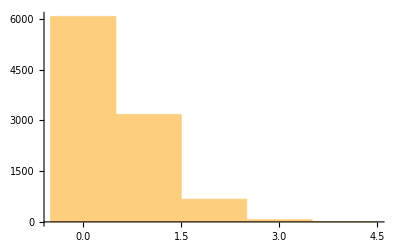

```mathematica
Histogram[Table[value[1,rerollNTimes[3,RandomInteger[{1,6},5],Function[{i,h},h[[i]]==6]]],{10000}],{1}]
```

```mathematica
hasPairAt[i_Integer,hand_List]:=Count[hand,hand[[i]]]>=2 (*keeps the numbers that appear at least twice.*)
```

```mathematica
N[Mean[Table[If[threeOfAKind[rerollNTimes[3,{1,1,2,2,4},hasPairAt]]>0,1,0],{100000}]]]
```

0.70358

```mathematica
rerollNTimes[1,{6,3,2,6,1},hasPairAt]
```

```mathematica
1/(6^5)(5^5+2*Binomial[5,2]*5^3+3*Binomial[5,3]*5^2+4*Binomial[5,4]*5^1+5)
```

5/6

```mathematica
(3(4!*2*5+4*Binomial[5,2]3!)-2*5!)/6^5
```

25/162

```mathematica
1200/7776
```

25/162

```mathematica
4/10*0+4/10*1+1.6/10*2
```

0.72